# Reševanje enačb in neenačb

Povzeto po: Bor Plestenjak: Tečaj iz Mathematice 2 in 5 del.
Priredila: Alen Orbanić, Matjaž Željko

## Eksaktno reševanje enačb

Glavni ukaz za eksaktno reševanje (sistemov) enačb je Solve. Ukaz Solve[en] poskusi rešiti sistem enačb en. Pri tem razume vse spremenljivke, ki nimajo prirejene vrednosti, kot neznanke. Rezultat vrne v obliki seznama podseznamov transformacijskih pravil. Vsak podseznam predstavlja eno od rešitev sistema. Če rešitev ne obstaja, vrne prazni seznam {}, če pa je rešitev poljubna, vrne seznam, ki vsebuje prazni seznam {{}}. Razširjeni verziji ukaza imata obliko Solve[en, neznanke] oziroma Solve[en, neznanke, domena], kjer je domena npr. Reals ali Integers.

```mathematica
Solve[x^2 == 1]
```

{{x→-1},{x→1}}

```mathematica
Solve[x-1 == x]
```

{}

```mathematica
Solve[x == x]
```

{{}}

```mathematica
p=2-2 x+x^2-x^3-x^4+x^5;
Solve[p==0, Integers]
Solve[p==0, Reals]
Solve[p==0]
Factor[p]
```

{{x→1}}

{{x→1},{x→-√2},{x→√2}}

{{x→-ⅈ},{x→ⅈ},{x→1},{x→-√2},{x→√2}}

(-1+x) (-2+x^2) (1+x^2)

Rešitve polinomskih enačb višjih stopenj lahko le izjemoma izrazimo z osnovnimi štirimi aritmetičnimi operacijami in korenjenjem.

```mathematica
Solve[x^5-4x+1==0]
Factor[x^5-4x+1]
```

{{x→Root[1-4 #1+#1^5&,1]},{x→Root[1-4 #1+#1^5&,2]},{x→Root[1-4 #1+#1^5&,3]},{x→Root[1-4 #1+#1^5&,4]},{x→Root[1-4 #1+#1^5&,5]}}

1-4 x+x^5

```mathematica
Solve[x^5+x-1==0]
Factor[x^5+x-1]
```

{{x→(-1)^(1/3)},{x→-(-1)^(2/3)},{x→1/3 (-1+(25/2-(3 √69)/2)^(1/3)+(1/2 (25+3 √69))^(1/3))},{x→-1/3-1/6 (1+ⅈ √3) (25/2-(3 √69)/2)^(1/3)-1/6 (1-ⅈ √3) (1/2 (25+3 √69))^(1/3)},{x→-1/3-1/6 (1-ⅈ √3) (25/2-(3 √69)/2)^(1/3)-1/6 (1+ⅈ √3) (1/2 (25+3 √69))^(1/3)}}

(1-x+x^2) (-1+x^2+x^3)

Enačba ali sistem enačb ima lahko tudi neskončno mnogo rešitev ...

```mathematica
Solve[Sin[x]==1/2,x]
```

{{x→ConditionalExpression[π/6+2 π C[1],C[1]∈Integers]},{x→ConditionalExpression[(5 π)/6+2 π C[1],C[1]∈Integers]}}

... ali pa se rešitve ne da zapisati v zaključeni obliki:

```mathematica
Solve[x==Tan[x]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[x==Tan[x]]

Sistem enačb podamo s seznamom enačb.

```mathematica
Solve[{x+y==2,x-y==3}]
```

{{x→5/2,y→-1/2}}

```mathematica
Solve[{x^2-y^2==1,x^2+y^2==4}]
```

{{x→-√(5/2),y→-√(3/2)},{x→-√(5/2),y→√(3/2)},{x→√(5/2),y→-√(3/2)},{x→√(5/2),y→√(3/2)}}

Če enačba oziroma sistem enačb poleg neznank(e) vsebuje še druge simbole (parametre), neznanko oziroma seznam neznank podamo kot drugi argument ukaza Solve.

```mathematica
Solve[a x+b==c]
```

{{c→b+a x}}

```mathematica
Solve[a x+b==c,x]
```

{{x→(-b+c)/a}}

```mathematica
Solve[a x+b==c,b]
```

{{b→c-a x}}

## Reševanje neenačb

Glavni ukaz za reševanje neenačb je ukaz Reduce, z njim pa lahko rešujemo tudi enačbe. 
Reduce[neen] poskusi rešiti neenačbo neen. Rezultat vrne v obliki unije enostavnih logičnih pogojev (npr. enostavnih neenakosti). Razširjena verzija ukaza ima obliko Reduce[neen, neznanke, domena], kjer je domena npr. Reals ali Integers.

```mathematica
Reduce[-2< x^3+x≤2]
```

-1<x≤1

```mathematica
Reduce[x^3+y^2<12,{x,y}]
```

x<2^(2/3) 3^(1/3)&&-√(12-x^3)<y<√(12-x^3)

Z ukazom Reduce lahko rešujemo tudi nekatere diofantske (celoštevilske) enačbe.

```mathematica
Reduce[7x+5y==23,{x,y},Integers]
```

C[1]∈Integers&&x==4+5 C[1]&&y==-1-7 C[1]

```mathematica
{%[[2,2]],%[[3,2]]}
```

{4+5 C[1],-1-7 C[1]}

```mathematica
%/.C[1]->k
```

{4+5 k,-1-7 k}

```mathematica
Table[Prepend[%,k],{k,-3,3}]
```

{{-3,-11,20},{-2,-6,13},{-1,-1,6},{0,4,-1},{1,9,-8},{2,14,-15},{3,19,-22}}

```mathematica
TableForm[%,TableHeadings->{{},{"k","x","y"}},TableAlignments->Right]
```

| k | x | y
 | -3 | -11 | 20
 | -2 | -6 | 13
 | -1 | -1 | 6
 | 0 | 4 | -1
 | 1 | 9 | -8
 | 2 | 14 | -15
 | 3 | 19 | -22

```mathematica
Reduce[x^2-7y^2==1&&x>0&&y>0,{x,y},Integers]
```

C[1]∈Integers&&C[1]≥1&&x==1/2 ((8-3 √7)^C[1]+(8+3 √7)^C[1])&&y==-((8-3 √7)^C[1]-(8+3 √7)^C[1])/(2 √7)

```mathematica
TableForm[Simplify[Table[Prepend[{%[[3,2]],%[[4,2]]}/.C[1]->k,k],{k,1,8}]],TableHeadings->{{},{"k","x","y"}},TableAlignments->Right]
```

| k | x | y
 | 1 | 8 | 3
 | 2 | 127 | 48
 | 3 | 2024 | 765
 | 4 | 32257 | 12192
 | 5 | 514088 | 194307
 | 6 | 8193151 | 3096720
 | 7 | 130576328 | 49353213
 | 8 | 2081028097 | 786554688

## Numerično reševanje enačb

Če želimo poiskati numerične rešitve enačb, uporabimo namesto ukaza Solve ukaz NSolve.

```mathematica
NSolve[x^5-4 x+1==0]
```

{{x→-1.47082},{x→-0.0613366-1.42087 ⅈ},{x→-0.0613366+1.42087 ⅈ},{x→0.250245},{x→1.34325}}

Obstajajo številne funkcije, katerih ničel se ne da eksaktno izračunati, lahko pa poiščemo poljubno natančne numerične približke. Oglejmo si reševanje naslednje enačbe:

```mathematica
NSolve[x ==Tan[x],x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[x==Tan[x],x]

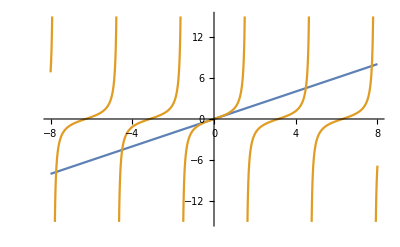

```mathematica
Plot[{x,Tan[x]},{x,-8,8}]
```

Funkcija FindRoot[en, {x, x0}] poišče numerični približek rešitve enačbe en z neznanko x, pri čemer za začetni približek vrednosti neznanke x vzame vrednost x0. Če rešujemo enačbo z več neznankami, sledijo še dodatni argumenti, ki so spet pari oblike {y, y0}, kjer je y0 začetni približek za vrednost neznanke y. Pri iskanju rešitve Mathematica naredi največ 100 iteracij, kar lahko spremenimo z izbirnim parametrom MaxIterations.

```mathematica
FindRoot[x ==Tan[x],{x,7}]
FindRoot[x ==Tan[x],{x,4}]
FindRoot[x ==Tan[x],{x,1}]
```

{x→7.72525}

{x→4.49341}

{x→2.63008×10^-8}

```mathematica
FindRoot[x ==Tan[x],{x,7}, WorkingPrecision-> 42, MaxIterations->256]
FindRoot[x ==Tan[x],{x,4}, WorkingPrecision-> 42, MaxIterations->256]
FindRoot[x ==Tan[x],{x,1}, WorkingPrecision-> 42, MaxIterations->256]
```

{x→7.72525183693770716419506893306298662637816}

{x→4.49340945790906417530788092728032208221558}

{x→2.26224046584052627940969886123994871962824×10^-21}